# Solving the 1D Heat Equation

Christopher Lum
lum@uw.edu

This document accompanies the YouTube video at https://youtu.be/I3jiMhVGmcg.

## Check That Total Solution Satisfies Initial Condition

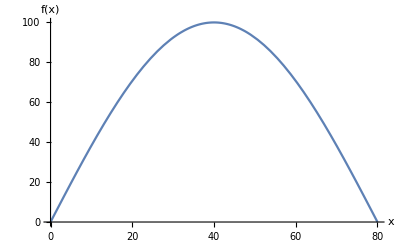

```mathematica
(*Input the initial condition*)
f[x_]=100 Sin[π x/80];

(*Visualize the function*)
Plot[f[x],{x,0,80},AxesLabel->{"x","f(x)"}]
```

```mathematica
(*Input problem constants*)
(*Define constants given by problem*)
ρ=8.92;
σ=0.092;
K=0.95;
L=80;

(*Compute intermediate variables*)
c=(K/(σ ρ))^(1/2)
```

1.07593

```mathematica
(*Define Subscript[λ, n]*)
λn[n_]=c n π/L

(*Define our total solution, u(x,t)*)
u[x_,t_]=100 Exp[-λn[1]^2 t] Sin[π/L x]
```

0.0422518 n

100 ⅇ^(-0.00178522 t) Sin[(π x)/80]

```mathematica
(*Verify u(x,t) satisfies original PDE*)
Print["Satisfies original PDE?"]
D[u[x,t],t]-c^2 D[u[x,t],{x,2}]==0//Chop

(*Verify u(x,t) satisfies boundary conditions*)
Print["Satisfies boundary conditions?"]
u[0,t]==0
u[L,t]==0

(*Verify that u(x,t) satisfies initial conditions*)
Print["Satisfies initial conditions?"]
u[x,0]==f[x]
```

Satisfies original PDE?

True

Satisfies boundary conditions?

True

True

Satisfies initial conditions?

True

We can now animate the scenario to obtain an idea of how the heat flows in this system.

```mathematica
(*Define parameters for the animation*)
tMax = 1500;
uMin=0;
uMax=100;

(*Animate the scenario*)
Manipulate[
Plot[u[x,t],{x,0,L},
PlotRange->{{0,L},{uMin,uMax}},
PlotLabel->"u(x,t)",
AxesLabel->{"x","u(x,t)"}],

{t,0,tMax}
]
```

Plot::plln: Limiting value L in {x,0,L} is not a machine-sized real number.